Autor: Dawid Bitner

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 4

Metoda predyktor-korektor

Napisać procedurę realizującą algorytm metody predyktor-korektor (argumenty:  f, x_0, y_0, b, n).
Jako metodę startową wykorzystać metodę Rungego-Kutty rzędu trzeciego. Jako metodę predykcji wykorzystać trzy krokową metodę Adamsa-Bashfortha, a jako metodę korekcji trzy krokową metodę Adamsa-Moultona. W metodzie korekcji wykonać dwie iteracje metody iteracji prostej.

Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=2 sin x - y(x),  x∈[0,15],
y(0)=2.

Obliczenia wykonać dla 20 i 100 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.
Wyznaczyć także błędy maksymalne oraz średnie dla obu siatek.

## Rozwiązanie

```mathematica
func[x_, y_]:=2*Sin[x]-y;
```

```mathematica
(* Metoda Rungego-Kutty rzędu trzeciego *)
rk3[f_,x0_,y0_,h_,n_]:=Module[{x,y,results},
x = x0;
y = y0;
results = {{x,y}};
Do[
k1 = f[x,y];
k2 =f[x+1/2 h, y +1/2 h*k1];
k3 = f[x+h,y-h*k1+2h*k2];
x = x + h;
y = y + 1/6 h*(k1 + 4k2 + k3);
AppendTo[results, {x,y}];
,{i,1, n}];
Return [results];
];
```

```mathematica
(* Metoda predyktor-korektor *)
pk[f_,x0_,y0_,b_,n_]:=Module[{
results,
x,y,yt,
h = (b-x0)/n,
ab31=23/12.,
ab32 = -16/12.,
ab33 = 5/12.,
am30= 9/24.,
am31=19/24.,
am32=-5/24.,
am33=1/24.
}, 
results = rk3[f, x0, y0, h, 3];
tempF = Table[f[results⟦i,1⟧, results⟦i,2⟧], {i, 1,3}];
x = Last[results]⟦1⟧;
y = Last[results]⟦2⟧;
Do[
yt = y+h*(ab31*tempF⟦3⟧+ab32*tempF⟦2⟧+ab33*tempF⟦1⟧);
Do[
yt =y + h*(am30*f[x,yt] + am31*tempF⟦3⟧+am32*tempF⟦2⟧+am33*tempF⟦1⟧);
,2];
y= yt;
x = x +h;
{ tempF⟦1⟧,tempF⟦2⟧,tempF⟦3⟧ } = { tempF⟦2⟧,tempF⟦3⟧, f[x,y] };
AppendTo[results, {x,y}];
,{i, 4, n}
];

Return[results];
];
```

```mathematica
(* Błąd maksymalny *)
bm[e_]:=Module[{},
Return[Sort[e //N, #1⟦2⟧ > #2⟦2⟧&]⟦1,2⟧];
];
```

```mathematica
(* Błąd średni *)
bs[e_]:=Module[{sum = 0,avg},
Do[
sum = sum + e⟦i,2⟧;
,{i, 1, Length[e]}
];

Return[sum/Length[e]];
];
```

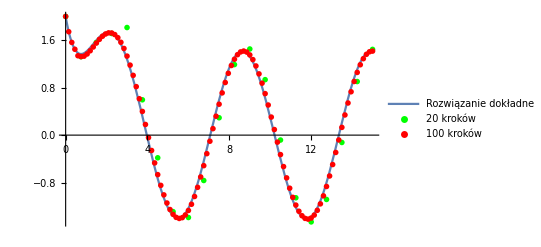

```mathematica
(* Rozwiązanie dokładne *)
result = DSolve[{y'[x]==2*Sin[x]-y[x], y[0]==2},y[x],x];
res = result⟦1,1,2⟧;
resultPlot = Plot[res, {x,0,15}, PlotRange->All, PlotLegends->LineLegend[{"Rozwiązanie dokładne"}]];
pk20 = pk[func, 0, 2, 15,20];
pk20Plot = ListPlot[pk20,PlotStyle->{PointSize[.01],Green}, PlotLegends->LineLegend[{"20 kroków"}]];
pk100 = pk[func, 0, 2, 15,100];
pk100Plot = ListPlot[pk100,PlotStyle->{PointSize[.01],Red}, PlotLegends->LineLegend[{"100 kroków"}]];
Show[resultPlot, pk20Plot,pk100Plot]
```

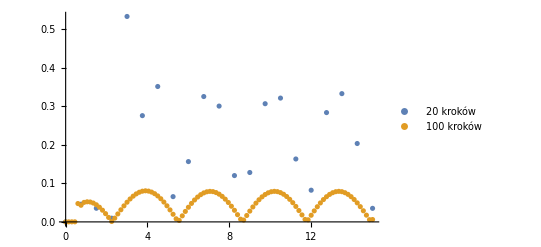

Największy błąd przy 20 krokach: 0.532976

Największy błąd przy 100 krokach: 0.080647

Średni błąd przy 20 krokach: 0.194045

Średni błąd przy 100 krokach: 0.0467336

```mathematica
(* Błędy *)
error20 = Table[{pk20⟦i,1⟧, Abs[(res/.x->pk20⟦i,1⟧)-pk20⟦i,2⟧]},{i, 1, Length[pk20]}];
error100 = Table[{pk100⟦i,1⟧, Abs[(res/.x->pk100⟦i,1⟧)-pk100⟦i,2⟧]},{i, 1, Length[pk100]}];
ListPlot[{error20, error100},  PlotLegends->{LineLegend[{"20 kroków", "100 kroków"}]},
PlotRange->All]
Print["Największy błąd przy 20 krokach: ",  bm[error20]];
Print["Największy błąd przy 100 krokach: ",  bm[error100]];
Print["Średni błąd przy 20 krokach: ",  bs[error20]];
Print["Średni błąd przy 100 krokach: ",  bs[error100]];
```